# NinePointCubic

Find a cubic plane curve that passes through nine given 2D points

## Definition

```mathematica
NinePointCubic[pts_]/;MatrixQ[pts]&&Dimensions[pts]==={9,2}:=NinePointCubic[pts,{x,y}];NinePointCubic[pts_,{xx_,yy_}]/;MatrixQ[pts]&&Dimensions[pts]==={9,2}:=Times@@Apply[Power,DeleteCases[FactorList[Det[PadLeft[Apply[Function[{x,y},{x,y,x^2,x y,y^2,x^3,x^2 y,x y^2,y^3}],Append[pts,{xx,yy}],{1}],{10,10},1]]],{_?NumericQ,_}],{1}]
```

## Documentation

### Usage

NinePointCubic[pts,{x,y}]

returns the implicit Cartesian equation in the variables x and y of the cubic plane curve that goes through the points pts.

NinePointCubic[pts]

uses the formal variables x and y.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Find a cubic plane curve through nine points:

```mathematica
BlockRandom[SeedRandom[1];
p9=RandomSample[Tuples[Range[-2,2],{2}],9]];
cubic=NinePointCubic[p9,{x,y}]
```

-20-24 x-x^2+3 x^3-28 y+6 x y-2 x^2 y+36 y^2+6 x y^2+24 y^3

Show the cubic and points:

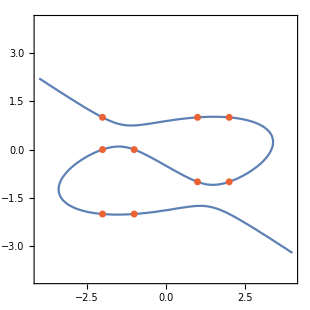

```mathematica
ContourPlot[cubic==0,{x,-4,4},{y,-4,4},Epilog->{,Point[p9]}]
```

### Scope

Find a cubic equation through nine points:

```mathematica
BlockRandom[SeedRandom[3];
p9=RandomSample[Tuples[Range[-2,2],{2}],9]];
cubic=NinePointCubic[p9,{x,y}]
```

-36-26 x+14 x^2+4 x^3-44 y-13 x y+13 x^2 y+9 y^2+2 x y^2+11 y^3

Show the cubic and points:

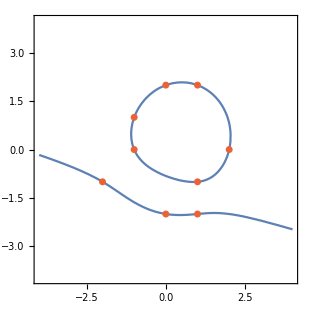

```mathematica
ContourPlot[cubic==0,{x,-4,4},{y,-4,4},Epilog->{,Point[p9]}]
```

Use formal variables:

```mathematica
NinePointCubic[p9]
```

-36-26 x+14 x^2+4 x^3-44 y-13 x y+13 x^2 y+9 y^2+2 x y^2+11 y^3

Find a cubic through nine points:

```mathematica
p9=Partition[RealDigits[N[1/19,18]][[1]],2];
cubic=NinePointCubic[p9,{x,y}]
```

(-1+x-2 y) (54-7 x+3 x^2-31 y-4 x y+5 y^2)

The cubic is factorizable and thus degenerate, and is composed of an ellipse and a line:

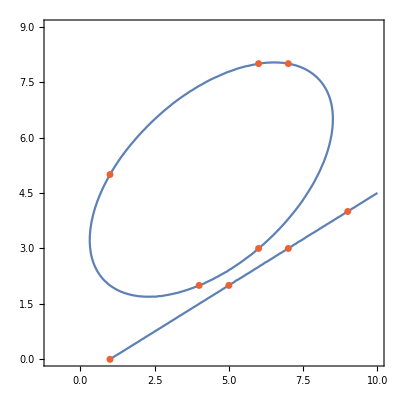

```mathematica
ContourPlot[cubic==0,{x,-1,10},{y,0,9},Epilog->{,Point[p9]}]
```

### Neat Examples

Some points and a cubic curve:

```mathematica
points={{0,0},{6,-6},{-6,6},{-2,-6},{2,6},{6,6},{-6,-6},{-6,0},{6,0},{0,3},{0,-3}};
cubic=NinePointCubic[RandomSample[points,9],{x,y}]
```

-324 x+9 x^3-36 y-3 x^2 y+4 y^3

Any line going through two points of a cubic will meet one of three criteria: 
1. it will go through a third point (gray),
2. it will be tangent at one of the points (red), or
3. it will be parallel with the cubics' asymptote (green), also called a point at infinity:

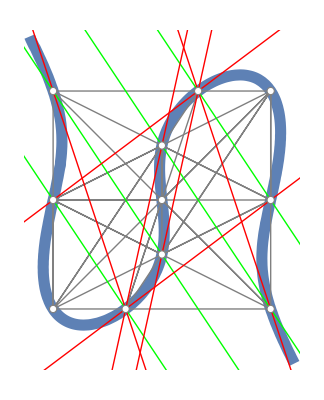

```mathematica
lines=ResourceFunction["FindExtraordinaryLines"][points];
linesinf={{2,10},{3,11},{4,8},{5,9}};
curve=ContourPlot[cubic==0,{x,-9,9},{y,-9,9},ContourStyle-> Thickness[.02]][[1]];
ordinary={{2,5},{3,4},{4,9},{4,10},{5,8},{5,11}};
Graphics[{curve,EdgeForm[Thick],Gray,Line[points[[#]]]&/@lines,Thick,
Green,InfiniteLine[points[[#]]]&/@linesinf,
Red,InfiniteLine[points[[#]]]&/@ordinary,
{White,Disk[#,.2]}&/@points}]
```

## Source & Additional Information

### Contributed By

Ed Pegg Jr

### Keywords

cubic plane curve

elliptic curve

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

ContourPlot

### Related Resource Objects

CubicSplineCurve

FormalizeSymbols

FivePointConic

NinePointQuadric

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.